# Project 5 - Bisection and Newton’s Method

## Bisection Method

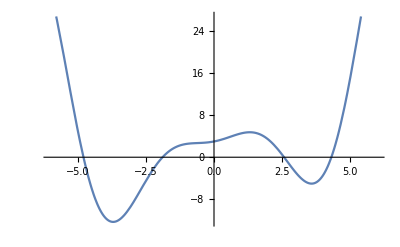

```mathematica
F[x_] := x^2 Cos[x]+x+3;
Plot[F[x],{x,-6,6}]
```

```mathematica
a= -4;
b= 2;
```

```mathematica
F[a]
N[F[a]]
```

-1+16 Cos[4]

-11.4583

```mathematica
F[b]
N[F[b]]
```

5+4 Cos[2]

3.33541

Since F[a]*F[b] < 0. There is a difference in signs, meaning that the function is discontinuous.

```mathematica
N[F[a]*F[b]] < 0
```

True

```mathematica
For[i=0,i<10,i++,Print[StringForm["Loop #: ``",i+1]];
c=(a+b)/2;
If[F[c]<0,a=c];
If[F[c]>0,b=c];
c=(a+b)/2;
Print[N[{"a = ",a,", b = ",b,", c = ",c,", F[c] = ",F[c]}]]]
```

Loop #: 1

{a = ,-4.,, b = ,-1.,, c = ,-2.5,, F[c] = ,-4.50715}

Loop #: 2

{a = ,-2.5,, b = ,-1.,, c = ,-1.75,, F[c] = ,0.704121}

Loop #: 3

{a = ,-2.5,, b = ,-1.75,, c = ,-2.125,, F[c] = ,-1.50142}

Loop #: 4

{a = ,-2.125,, b = ,-1.75,, c = ,-1.9375,, F[c] = ,-0.283426}

Loop #: 5

{a = ,-1.9375,, b = ,-1.75,, c = ,-1.84375,, F[c] = ,0.239846}

Loop #: 6

{a = ,-1.9375,, b = ,-1.84375,, c = ,-1.89063,, F[c] = ,-0.0144502}

Loop #: 7

{a = ,-1.89063,, b = ,-1.84375,, c = ,-1.86719,, F[c] = ,0.114541}

Loop #: 8

{a = ,-1.89063,, b = ,-1.86719,, c = ,-1.87891,, F[c] = ,0.0505051}

Loop #: 9

{a = ,-1.89063,, b = ,-1.87891,, c = ,-1.88477,, F[c] = ,0.0181423}

Loop #: 10

{a = ,-1.89063,, b = ,-1.88477,, c = ,-1.8877,, F[c] = ,0.00187477}

To find the estimate of c where F(c) = 0, we take the absolute value of the difference of a and b for all ten loops. Only one loop exist where the lowest absolute value of the difference was less than 0.01. That value of c = -1.8877 will result in the lowest value of of F[c] in the 10 resulting loops, which is F[c] = 0.0018.

```mathematica
If[Abs[a-b]≤ 0.01,Print[N[c]],Exit[]]
```

-1.8877

## Newton’s Method

```mathematica
a=-3;
```

```mathematica
For[i=1,i≤5,i++,
a = a - F[a]/F'[a];];
Print@Row[{"c = ",N[a],", F[c] = ",N[F[a]]}]
```

c = -1.88803, F[c] = -2.22045×10^-16

Using Newton’s Method, we were able to achieve a more accurate value of c where F[c] is closer to 0 than the Bisection method. In the loop of 5 iterates, c = -1.8803 has a F[c] = -2.22045 * 10^-16 which is closer than the values found using the Bisection method where c = -1.8877 and F[c] = 0.00187477.

## Numerical Newton’s Method

```mathematica
h= 0.001;
g[x_] := (F[x+h]-F[x])/h;
```

```mathematica
For[i=1,i≤5,i++,
a = a - F[a]/g[a];];
Print@Row[{"c = ",N[a],", F[c] = ",N[F[a]]}]
```

c = -1.88803, F[c] = 0.

This version of the algorithm using the derivative of F was able to find c where F[c] = 0. Whereas, the other methods were only able to approximate.

## Building a Function Call

```mathematica
Clear[bisectionMethod];
bisectionMethod[f_,a_,b_, n_]:=Module[{a0,b0,c,y},
a0=a;
b0=b;
c=(a0+b0)/2;
For[i=0,i<n,i++,Print[StringForm["Loop #: ``",i+1]];
y=f[c];
If[y<0,a0=c,If[y>0,b0=c,Break[]]];
c=(a0+b0)/2;
x = f[a0];
z=f[b0];
Print [{{N[a0],N[b0]},{N[x],N[z]}}]
]
]
```

## Problems with Newton’s Method

```mathematica
Clear[x0,x1,x,H,k]
H[x_] := ArcTan[x];
k[x_] := (H[x+h]-H[x])/h;
x0=0.5;
h=0.001;
For[i=1,i≤ 10,i+1, Print["Loop #:", i++];
x= x0- H[x0]/k[x0];
x0=x;
Print[{x,H[x]}]]
```

Loop #:1

{-0.0797915,-0.0796228}

Loop #:2

{0.000331914,0.000331914}

Loop #:3

{-2.45182×10^-10,-2.45182×10^-10}

Loop #:4

{8.17273×10^-17,8.17273×10^-17}

Loop #:5

{-2.72424×10^-23,-2.72424×10^-23}

Loop #:6

{9.08081×10^-30,9.08081×10^-30}

Loop #:7

{-3.02693×10^-36,-3.02693×10^-36}

Loop #:8

{1.00898×10^-42,1.00898×10^-42}

Loop #:9

{-3.36326×10^-49,-3.36326×10^-49}

Loop #:10

{1.12109×10^-55,1.12109×10^-55}

```mathematica
Clear[x0,x1,x,H,k]
H[x_] := ArcTan[x];
k[x_] := (H[x+h]-H[x])/h;
x0=2.0;
h=0.001;
For[i=1,i≤ 10,i+1, Print["Loop #:", i++];
x= x0- H[x0]/k[x0];
x0=x;
Print[{x,H[x]}]]
```

Loop #:1

{-3.53796,-1.29533}

Loop #:2

{13.9667,1.49932}

Loop #:3

{-280.022,-1.56723}

Loop #:4

{122611.,1.57079}

Loop #:5

{-2.36594×10^10,-1.5708}

Loop #:6

Power::infy: Infinite expression 1/0. encountered.

{ComplexInfinity,Indeterminate}

Loop #:7

{Indeterminate,Indeterminate}

Loop #:8

{Indeterminate,Indeterminate}

Loop #:9

{Indeterminate,Indeterminate}

Loop #:10

{Indeterminate,Indeterminate}

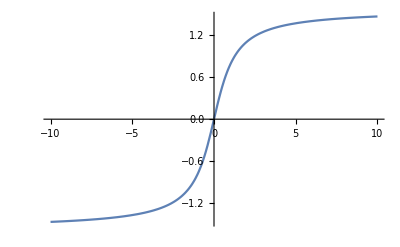

```mathematica
Plot[H[x],{x,-10,10}]
```

Arctan(x) with initial condition at x = 2 is indeterminate after the fifth loop and there is an error in recursion. This occurred  because Newton’s method generate a sequence {x_n} with alternating signs that are the same distance from the origin. (x_n+1 = -x_n). However, after the fifth loop, it fails because x_n+1 > x_n and the derivative of G is 0. Dividing by G’(x) = 0 will result in an indeterminate answer. This can be seen in the graph where the graph flattens out, creating a horizontal tangent line.

```mathematica
Clear[x0,x1,x,G,l,h]
G[x_]:= Sign[x]*(Abs[x])^(1/3);
l[x_] := (G[x+h]-G[x])/h;
x0=1.0;
h=0.001;
For[i=1,i≤ 10,i+1, Print["Loop #:", i++];
x= x0- G[x0]/l[x0];
x0=x;
Print[{x,G[x]}]]
```

Loop #:1

{-2.001,-1.26013}

Loop #:2

{4.001,1.58753}

Loop #:3

{-8.003,-2.00025}

Loop #:4

{16.005,2.5201}

Loop #:5

{-32.011,-3.17517}

Loop #:6

{64.021,4.00044}

Loop #:7

{-128.043,-5.04025}

Loop #:8

{256.085,6.35031}

Loop #:9

{-512.171,-8.00089}

Loop #:10

{1024.34,10.0805}

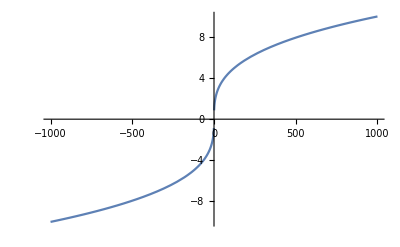

```mathematica
Plot[G[x],{x,-1000,1000}]
```

The function is growing without converging at a root. The sequence for this  function is x_n = ((-1)^n)*(2^(n-1)). This mean that no matter what the initial point x0 is, the function is rapidly increasing, moving further away from the root and diverges.